```mathematica
Manipulate[N[Sum[(-1)^n a^n Exp[μ (Exp[-n]-1)],{n,0,10}]],{{a,1},0.5,2},{{μ,5},1,100}]
```

```mathematica
Manipulate[N[Sum[(-1)^n a^n(1+μ/T(Exp[-n]-1))^T,{n,0,10}]],{{a,1},0.5,2},{{μ,5},1,100},{{T,100},50,1000}]
```

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[n-1,y]]
Expectation[(x-(-1+n) y)^2,x\[Distributed]NormalDistribution[(n-1)y,√((n-1)y(1-y))]]//Simplify
```

(-1+n) y

y (-1+n+y-n y)

```mathematica
D[1/(1+Exp[σ-β (1+x)/n]) ,{x,2}]//Simplify
```

(ⅇ^(((1+x) β)/n+σ) (-ⅇ^(((1+x) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+x) β)/n)+ⅇ^σ)^3 n^2)

```mathematica
(ⅇ^(((1+x) β)/n+σ) (-ⅇ^(((1+x) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+x) β)/n)+ⅇ^σ)^3 n^2)/.{x->(-1+n) y}//Simplify
```

(ⅇ^(((1+(-1+n) y) β)/n+σ) (-ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ)^3 n^2)

```mathematica
Series[1/2(ⅇ^(y β+(y β)/n+σ) (-ⅇ^(y β)+ⅇ^((y β)/n+σ)) β^2)/((ⅇ^(y β)+ⅇ^((y β)/n+σ))^3 n^2)(n-1)y(1-y),{n,Infinity,1}]//Simplify
```

-(ⅇ^(y β+σ) (-ⅇ^(y β)+ⅇ^σ) (-1+y) y β^2)/(2 (ⅇ^(y β)+ⅇ^σ)^3 n)+O[1/n]^2

```mathematica
-(ⅇ^(y β+σ) (-ⅇ^(y β)+ⅇ^σ) (-1+y) y β^2)/(2 (ⅇ^(y β)+ⅇ^σ)^3 n)//TeXForm
```

```mathematica
D[1/(1+Exp[σ-β (1+x)/n]) ,{x,2}]//Simplify
```

(ⅇ^(((1+x) β)/n+σ) (-ⅇ^(((1+x) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+x) β)/n)+ⅇ^σ)^3 n^2)

```mathematica
(ⅇ^(((1+x) β)/n+σ) (-ⅇ^(((1+x) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+x) β)/n)+ⅇ^σ)^3 n^2)/.{x->(-1+n) y}//Simplify
```

(ⅇ^(((1+(-1+n) y) β)/n+σ) (-ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ) β^2)/((ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ)^3 n^2)

```mathematica
Series[(ⅇ^(y β+σ) (-ⅇ^(y β)+ⅇ^σ) (1-y) y β^2)/(2 (ⅇ^(y β)+ⅇ^σ)^3 n),{β,0,1}]//Simplify
```

-((ⅇ^σ (-1+ⅇ^σ) (-1+y) y) β^2)/(2 ((1+ⅇ^σ)^3 n))+O[β]^3

```mathematica
{α,β,σ,n,κ,δ}=.;
Gp2[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))+α(1+Exp[σ])(ⅇ^(((1+(-1+n) y) β)/n+σ) (-ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ) β^2(n-1)y(1-y))/(2(ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ)^3 n^2)-κ;
Gn2[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]))+α(1+Exp[σ])(ⅇ^((((-1+n) y) β)/n+σ) (-ⅇ^((((-1+n) y) β)/n)+ⅇ^σ) β^2(n-1)y(1-y))/(2(ⅇ^((((-1+n) y) β)/n)+ⅇ^σ)^3 n^2);
dydt2[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=y(1-y)(1-Y)(Gp2[y,α,β,σ,n,κ] -Gn2[y,α,β,σ,n,κ]);
dYdt2[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=-Y(δ-(1-Y)(Gp2[y,α,β,σ,n,κ] y+Gn2[y,α,β,σ,n,κ](1-y)));
Y2[y0_,α_,β_,σ_,n_,κ_,δ_]:=1-δ/(Gp2[y0,α,β,σ,n,κ] y0+Gn2[y0,α,β,σ,n,κ](1-y0));
J2[y0_,Y0_,α_,β_,σ_,n_,κ_,δ_]=D[{dydt2[y0,Y0,α,β,σ,n,κ,δ],dYdt2[y0,Y0,α,β,σ,n,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,n_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J2[y0,Y2[y0,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ];
```

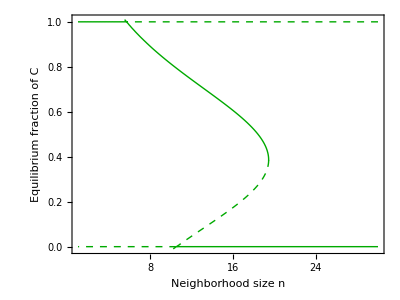

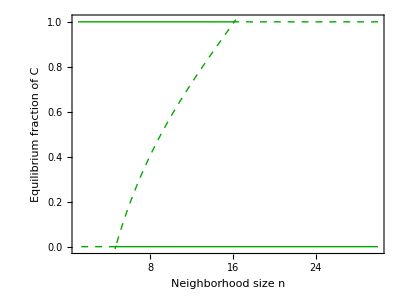

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,β,σ,κ,δ}={1,5,2,0.5,0.1};
Show[
D3=ContourPlot[dydt2[y,Y2[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Darker[Green],Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50
],

D4=ContourPlot[dydt2[y,Y2[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Darker[Green]}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50]
]
{α,β,σ,κ,δ}={1,2,3,0.5,0.1};
Show[
C3=ContourPlot[dydt2[y,Y2[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Darker[Green],Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50
],

C4=ContourPlot[dydt2[y,Y2[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Darker[Green]}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50]
]
```

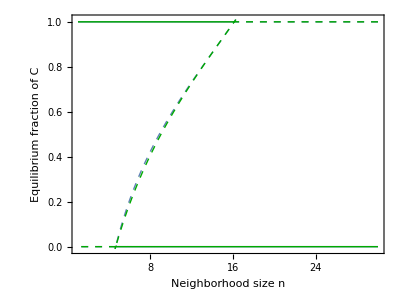

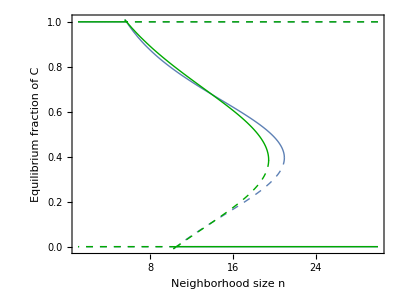

```mathematica
Show[C1,C2,C3,C4]
Show[D1,D2,D3,D4]
```